# Benthic v. Pelagic Encounter Rates

Eden Forbes, 2026

```mathematica
ClearAll["Global`*"]
```

## Functions

### Benthic ER

```mathematica
(* Circles & Velo *)
Aint[d_, z_]:= 2 d^2 ArcCos[z/(2 d)]-z/2 √(4 d^2-z^2);

EINT[d_, P_, u_, z_, s_, r_]:=((Pi d^2 P+2d P u r)/(s+r))(1-Aint[d,z]/(Pi d^2))+2d P u (Aint[d,z]/(Pi d^2));
```

### Pelagic ER

#### Stationary

```mathematica
E2DS[d_,P_,v_]:= 2 d P v;
E3DS[d_,P_,v_]:=  π d^2 P v;
```

#### Mobile

```mathematica
E2DM[d_,P_,u_,v_]:=2 d P Sqrt[u^2+v^2]
E3DM[d_,P_,u_,v_]:=π d^2 P Sqrt[u^2+v^2]
```

```mathematica
M2Do[dens_, v_,u_,rad_]:=1/π 2 dens rad (√((u-v)^2) EllipticE[-(4 u v)/(u-v)^2]+√((u+v)^2) EllipticE[(4 u v)/(u+v)^2]);
M3Do[dens_,v_,u_,rad_]:=  Piecewise[{{(π rad^2 dens)/3((u^2+3 v^2)/v), u<v},{(π rad^2 dens)/3((v^2+3 u^2)/u), u >= v}}];
```

### Functional responses

```mathematica
T2[er_,es_,h_] := (er es)/(1 + er es h);(* Encounter rate accounts for density *)
```

### Utility

```mathematica
restylePlot[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]]
```

## Encounter Rates

#### E2DM

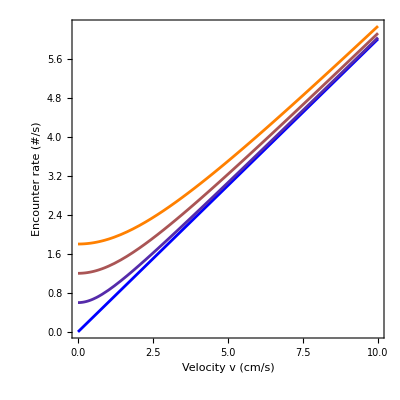

```mathematica
Plot[Evaluate@Table[Style[E2DM[30,0.01,u,v],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{v,0,10}, 
PlotRange->{All, {-0.2,All}},AspectRatio->1, Frame->True,FrameLabel->{"Velocity v (cm/s)","Encounter rate (#/s)"}, LabelStyle->{Black,20}]
```

#### E3DM

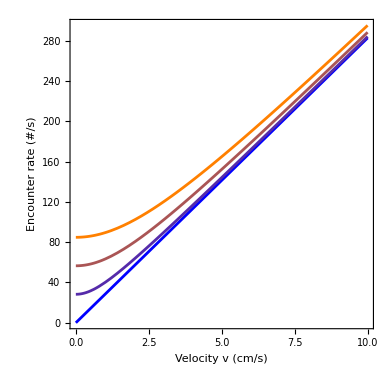

```mathematica
Plot[Evaluate@Table[Style[E3DM[30,0.01,u,v],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{v,0,10}, 
PlotRange->{All, {-0.2,All}},AspectRatio->1, Frame->True,FrameLabel->{"Velocity v (cm/s)","Encounter rate (#/s)"}, LabelStyle->{Black,20}]
```

#### EINT

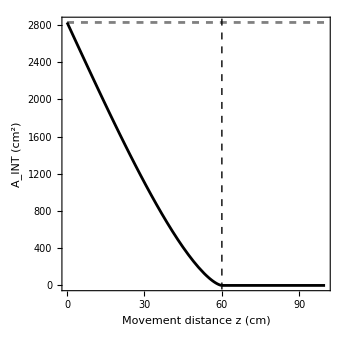

```mathematica
Show[
Plot[Pi 30^2,{z,0,100}, PlotStyle->{Gray, Dashed}],
Plot[Re[Aint[30,z]],{z,0,100}, PlotStyle->Black],
Graphics[{Dashed, Black, InfiniteLine[{{60,0},{60,50}}]}],
PlotRange->All, AspectRatio->1, Frame->True,FrameLabel->{"Movement distance z (cm)","A_INT (cm^2)"},LabelStyle->{18,Black}
]
```

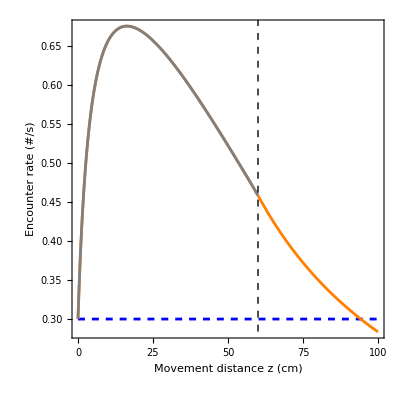

```mathematica
(* Prey speed *)
Show[
Plot[Re[EINT[30, 0.01,0.5, 0, 0, 5]],{z,0,100},PlotStyle->{Blue, Dashed}],
Plot[Re[EINT[30, 0.01, 0.5, z, z, 5]],{z,0,100},PlotStyle->Orange],
Plot[Re[EINT[30, 0.01, 0.5, z, z, 5]],{z,0,60},PlotStyle->Gray,PlotRange->All],  
Graphics[{Dashed, Black, InfiniteLine[{{60,0},{60,50}}]}],
Graphics[{Thin,Black, InfiniteLine[{{0,0},{50,0}}]}],
PlotRange->{All,{0,All}},AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Movement distance z (cm)","Encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
Maximize[{Re[EINT[30, 0.01, 0, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 2, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.02, 3, z, z, 5]],z>0},z]
```

{0.493551,{z→34.1185}}

{0.914434,{z→10.9413}}

{1.44548,{z→6.91329}}

{4.00874,{z→5.1624}}

```mathematica
preyspeed = {
{34.12,Re[EINT[30, 0.01, 0, 34.12, 34.12, 5]]},
{10.94,Re[EINT[30, 0.01, 1, 10.94, 10.94, 5]]},
{6.91,Re[EINT[30, 0.01, 2, 6.91, 6.91, 5]]},
{5.16,Re[EINT[30, 0.01, 3, 5.16, 5.16, 5]]}
};
```

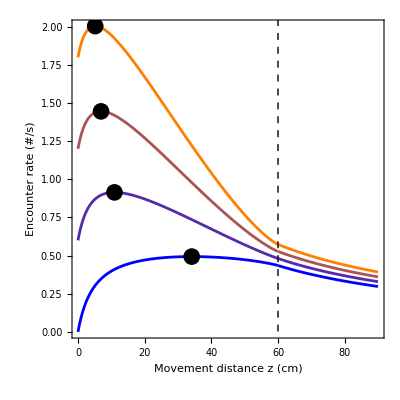

```mathematica
(* Prey speed *)
Show[
Graphics[{Dashed, Black, InfiniteLine[{{60,0},{60,50}}]}],
Plot[Evaluate@Table[Style[Re[EINT[30, 0.01, u, z, z, 5]],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{z,0,90}],
ListPlot[preyspeed,PlotStyle->{Black,PointSize[0.03]}],
PlotRange->All,AspectRatio->1, Frame->True,FrameLabel->{"Movement distance z (cm)","Encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
Maximize[{Re[EINT[30, 0.01, 1, z, z, 1]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 1, z, z, 6]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 1, z, z, 11]],z>0},z]
Maximize[{Re[EINT[30, 0.02, 1, z, z, 16]],z>0},z]
```

{1.04809,{z→5.87132}}

{0.896243,{z→11.6286}}

{0.834017,{z→13.9798}}

{1.59181,{z→15.422}}

```mathematica
resttime = {
{5.87,Re[EINT[30, 0.01, 1, 5.87, 5.87, 1]]},
{11.63,Re[EINT[30, 0.01, 1, 11.63, 11.63, 6]]},
{13.98,Re[EINT[30, 0.01, 1,13.98, 13.98, 11]]},
{15.42,Re[EINT[30, 0.01, 1, 15.42, 15.42, 16]]}
};
```

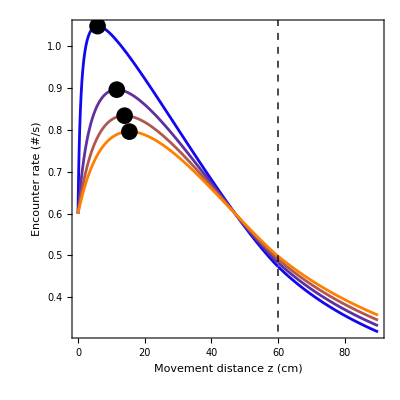

```mathematica
(* Rest time *)
Show[
Graphics[{Dashed, Black, InfiniteLine[{{60,0},{60,50}}]}],
Plot[Evaluate@Table[Style[Re[EINT[30, 0.01, 1, z, z, r]],Blend[{Blue,Orange},r/16]],{r,1,16,5}],{z,0,90}],
ListPlot[resttime,PlotStyle->{Black,PointSize[0.03]}],
PlotRange->{All,{0.2,All}},AspectRatio->1, Frame->True,FrameLabel->{"Movement distance z (cm)","Encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
Maximize[{Re[EINT[30, 0.01, 1, z, 2*z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 1, z, 1.5*z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.01, 1, z, 0.5*z, 5]],z>0},z]
```

{0.757887,{z→5.54614}}

{0.810283,{z→7.36844}}

{0.914434,{z→10.9413}}

{1.21865,{z→20.7694}}

```mathematica
velocity = {
{20.77,Re[EINT[30, 0.01, 1, 20.77, 0.5*20.77, 5]]},
{10.94,Re[EINT[30, 0.01, 1, 10.94, 10.94, 5]]},
{7.37,Re[EINT[30, 0.01, 1,7.37, 1.5*7.37, 5]]},
{5.55,Re[EINT[30, 0.01, 1, 5.55,2.0* 5.55, 5]]}
};
```

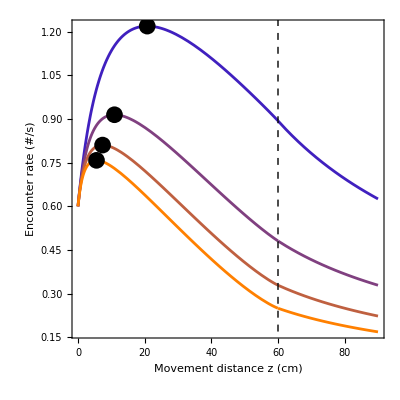

```mathematica
(* Movement time / predator speed *)
Show[
Graphics[{Dashed, Black, InfiniteLine[{{60,0},{60,50}}]}],
Plot[Evaluate@Table[Style[Re[EINT[30, 0.01, 1, z, a*z, 5]],Blend[{Blue,Orange},a/2]],{a,0.5,2,0.5}],{z,0,90}],
ListPlot[velocity,PlotStyle->{Black,PointSize[0.03]}],
PlotRange->All,AspectRatio->1, Frame->True,FrameLabel->{"Movement distance z (cm)","Encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
Maximize[{Re[EINT[30, 0.01, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.04, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.07, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[30, 0.011, 1, z,z, 5]],z>0},z]
```

{0.914434,{z→10.9413}}

{3.65773,{z→10.9413}}

{6.40104,{z→10.9413}}

{1.00588,{z→10.9413}}

```mathematica
density = {
{10.94,Re[EINT[30, 0.01, 1, 10.94,10.94, 5]]},
{10.94,Re[EINT[30, 0.04, 1, 10.94, 10.94, 5]]},
{10.94,Re[EINT[30, 0.07, 1,10.94, 10.94, 5]]},
{10.94,Re[EINT[30, 0.1, 1, 10.94,10.94, 5]]}
};
```

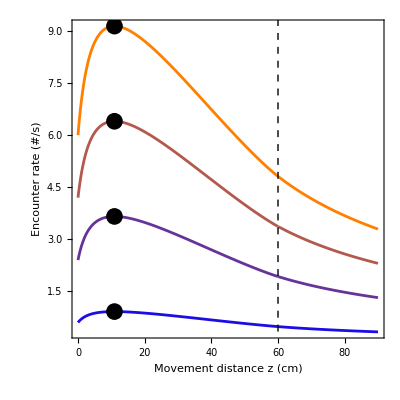

```mathematica
(* Prey density *)
Show[
Graphics[{Dashed, Black, InfiniteLine[{{60,0},{60,50}}]}], 
Plot[Evaluate@Table[Style[Re[EINT[30, P, 1, z, z, 5]],Blend[{Blue,Orange},P/0.1]],{P,0.01,0.1,0.03}],{z,0,90}],
ListPlot[density,PlotStyle->{Black,PointSize[0.03]}],
PlotRange->All,AspectRatio->1, Frame->True,FrameLabel->{"Movement distance z (cm)","Encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
Maximize[{Re[EINT[1, 0.01, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[11, 0.01, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[21, 0.01, 1, z, z, 5]],z>0},z]
Maximize[{Re[EINT[31, 0.01, 1, z,z, 5]],z>0},z]
```

{0.0213336,{z→0.712556}}

{0.297736,{z→5.43116}}

{0.614966,{z→8.60862}}

{0.948249,{z→11.18}}

```mathematica
detection= {
{0.71,Re[EINT[1, 0.01, 1, 0.71,0.71, 5]]},
{5.43,Re[EINT[11, 0.01, 1,5.43, 5.43, 5]]},
{8.61,Re[EINT[21, 0.01, 1,8.61, 8.61, 5]]},
{11.18,Re[EINT[31, 0.01, 1, 11.18,11.18, 5]]}
};
```

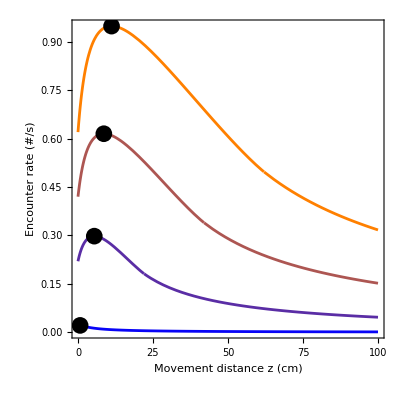

```mathematica
(* Detection radius *)
Show[
Plot[Evaluate@Table[Style[Re[EINT[d, 0.01, 1, z, z, 5]],Blend[{Blue,Orange},d/31]],{d,1,31,10}],{z,0,100}],
ListPlot[detection,PlotStyle->{Black,PointSize[0.03]}],
PlotRange->All,AspectRatio->1, Frame->True,FrameLabel->{"Movement distance z (cm)","Encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

## Comparisons: E2DM & E3DM

```mathematica
densScalar=4;
```

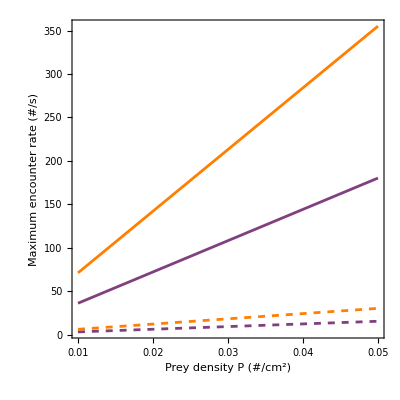

```mathematica
(* Prey density *)
Show[
Plot[Evaluate@Table[Style[E3DM[30,P/densScalar,1,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{P,0.01,0.05}],
Plot[Evaluate@Table[Style[E2DM[30,P,1,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{P,0.01,0.05}, PlotStyle->Dashed],
PlotRange->{{0.01,All},All},AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Prey density P (#/cm^2)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

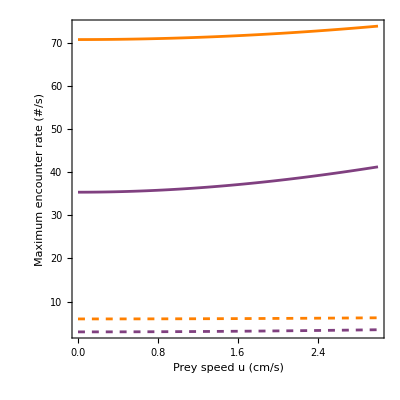

```mathematica
(* Prey speed *)
Show[
Plot[Evaluate@Table[Style[E3DM[30,0.01/densScalar,u,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{u,0,3}],
Plot[Evaluate@Table[Style[E2DM[30,0.01,u,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{u,0,3}, PlotStyle->Dashed],
PlotRange->All,AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Prey speed u (cm/s)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

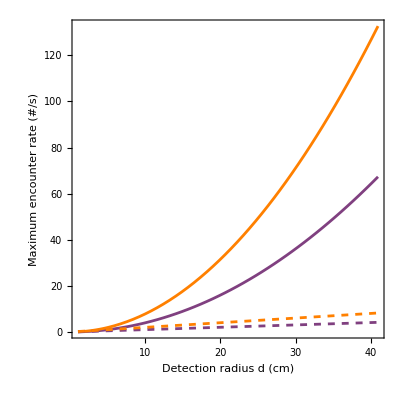

```mathematica
(* Prey speed *)
Show[
Plot[Evaluate@Table[Style[E3DM[d,0.01/densScalar,1,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{d,1,41}],
Plot[Evaluate@Table[Style[E2DM[d,0.01,1,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{d,1,41}, PlotStyle->Dashed],
PlotRange->All,AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Detection radius d (cm)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

## Comparisons: E2DM & EINT

```mathematica
gran = 0.001; min = 0.01; max = 0.05;  ZP = List[]; EINTP = List[];
For[i=min/gran,i<=max/gran,i++,
zmax = Maximize[{Re[EINT[30, i*gran, 1, z, z, 5]],z>0},z][[2]][[1]][[2]];
AppendTo[ZP,{i*gran,zmax}];
AppendTo[EINTP,{i*gran,EINT[30, i*gran, 1, zmax, zmax, 5]}];
]
```

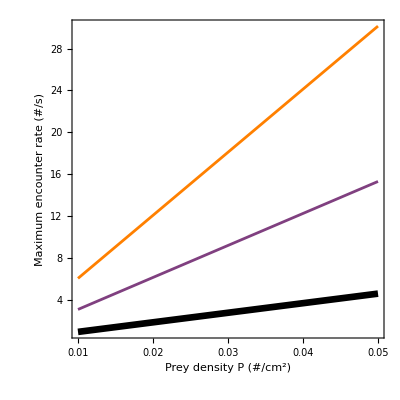

```mathematica
(* Prey density *)
Show[
Plot[Evaluate@Table[Style[E2DM[30,P,1,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{P,0.01,0.05}],
ListLinePlot[EINTP,PlotStyle->{Black,Thickness[0.012]}], 
PlotRange->{{0.01,All},All},AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Prey density P (#/cm^2)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
gran = 0.1; min = 0; max = 3; ZU=List[]; EINTU = List[];
For[i=min/gran,i<=max/gran,i++,
zmax = Maximize[{Re[EINT[30, 0.01, i*gran, z, z, 5]],z>0},z][[2]][[1]][[2]];
AppendTo[ZU,{i*gran,zmax}];
AppendTo[EINTU,{i*gran,EINT[30,0.01, i*gran, zmax, zmax, 5]}];
]
```

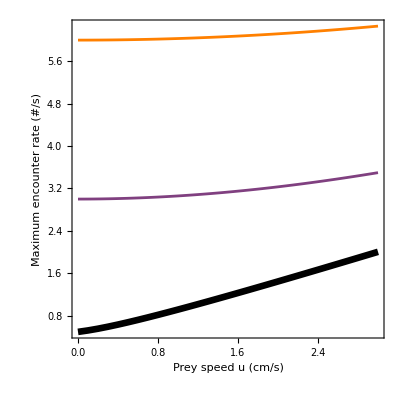

```mathematica
(* Prey speed *)
Show[
Plot[Evaluate@Table[Style[E2DM[30,0.01,u,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{u,0,3}],
ListLinePlot[EINTU,PlotStyle->{Black,Thickness[0.012]}], 
PlotRange->All,AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Prey speed u (cm/s)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

```mathematica
gran =1; min = 1; max = 31; ZD=List[];EINTD = List[];
For[i=min/gran,i<=max/gran,i++,
zmax = Maximize[{Re[EINT[i*gran, 0.01, 1, z, z, 5]],z>0},z][[2]][[1]][[2]];
AppendTo[ZD,{i*gran,zmax}];
AppendTo[EINTD,{i*gran,EINT[i*gran,0.01, 1, zmax, zmax, 5]}];
]
```

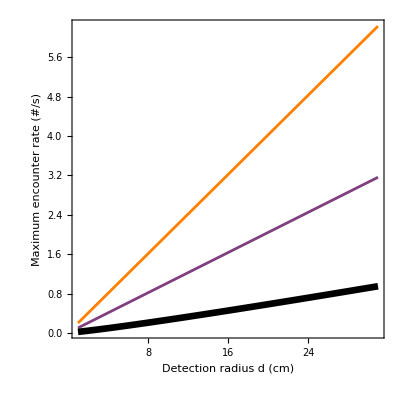

```mathematica
(* Prey speed *)
Show[
Plot[Evaluate@Table[Style[E2DM[d,0.01,1,v],Blend[{Blue,Orange},v/10]],{v,5,10,5}],{d,1,31}],
ListLinePlot[EINTD,PlotStyle->{Black,Thickness[0.012]}], 
PlotRange->All,AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Detection radius d (cm)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

## Comparisons: EINT & E3DM

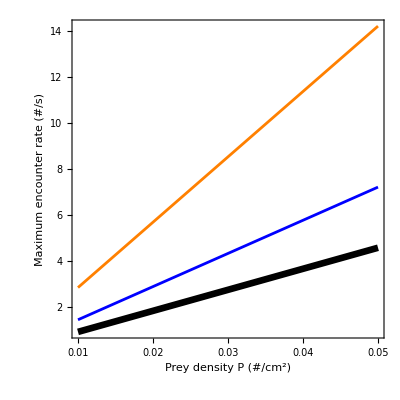

```mathematica
(* Prey density *)
Show[
Plot[E3DM[30,P/densScalar,1,5],{P,0.01,0.05}, PlotStyle->Blue],
Plot[E3DM[30,P/densScalar,1,10],{P,0.01,0.05}, PlotStyle->Orange],
ListLinePlot[EINTP,PlotStyle->{Black,Thickness[0.012]}], 
PlotRange->{{0.01,All},All},AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Prey density P (#/cm^2)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,20}
]
```

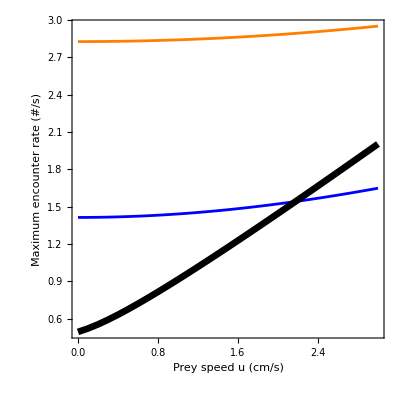

```mathematica
(* Prey speed *)
Show[
Plot[E3DM[30,0.01/densScalar,u,5],{u,0,3}, PlotStyle->Blue],
Plot[E3DM[30,0.01/densScalar,u,10],{u,0,3}, PlotStyle->Orange],
ListLinePlot[EINTU,PlotStyle->{Black,Thickness[0.012]}], 
PlotRange->All,AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Prey speed u (cm/s)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,24}
]
```

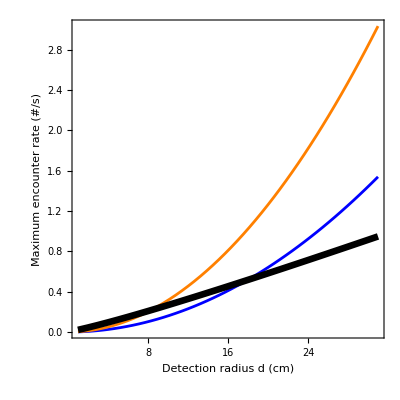

```mathematica
(* Prey speed *)
Show[
Plot[E3DM[d,0.01/densScalar,1,5],{d,1,31}, PlotStyle->Blue],
Plot[E3DM[d,0.01/densScalar,1,10],{d,1,31}, PlotStyle->Orange],
ListLinePlot[EINTD,PlotStyle->{Black,Thickness[0.012]}], 
PlotRange->{{1,All},All},AspectRatio->1, Frame->True,AxesOrigin->{0,0},FrameLabel->{"Detection radius d (cm)","Maximum encounter rate (#/s)"}, LabelStyle->{Black,24}
]
```

## Application to Freshwater Fishes

```mathematica
densScalar = 4;
(* Population Constants *)
sculN =0.0218; (* Sculpin population density (#/m^2) - at 90+m, Forbes et al. (2026) *)
smeltN =0.0021; (* Smelt population density (#/m^3) - based on CPUE from with a 5x5m net at 91.67 m/s for 55min from Main Lake in Bruel et al. (2021) *)

(* Size Constants *)
sculD = 29.0; (* Sculpin detection radius in cm - Janssen (1990) *)
smeltL = 14.0;  (* Coughlin et al. (1999)*)
smeltD = smeltL^1.1;  (* Smelt detection radius in cm - Ware (1978) *)

(* Motion Constants *)
mv = 1.5;  (* ~0.5-5,
 Small mysid velocity in cm/sec - Bowers et al.(1990) *)
smeltv = 10;
```

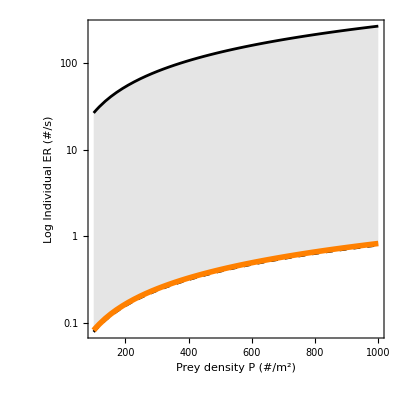

```mathematica
(* Prey density *)
Show[
LogPlot[{E3DM[smeltD,P/10000/densScalar,mv,smeltv],E3DM[1,P/10000/densScalar,mv,smeltv]},{P,100,1000},Filling->{1->{2}},FillingStyle->Opacity[0.1],PlotStyle->{Black, {Black,Dashed}}],

LogPlot[Re[EINT[13, P/10000, 0, 3, 0.6, 8.8]],{P,100,1000},PlotStyle->{Orange, Thickness[0.01]}], 
PlotRange->{All,All},AspectRatio->1, Frame->True,FrameLabel->{"Prey density P (#/m^2)","Log Individual ER (#/s)"}, LabelStyle->{Black,16}
]
```

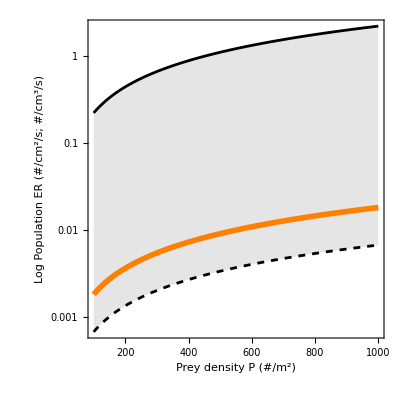

```mathematica
(* Prey density *)
Show[
LogPlot[{4*smeltN*E3DM[smeltD,P/10000/densScalar,mv,smeltv],4*smeltN*E3DM[1,P/10000/densScalar,mv,smeltv]},{P,100,1000},Filling->{1->{2}},FillingStyle->Opacity[0.1],PlotStyle->{Black, {Black,Dashed}}],

LogPlot[Re[(sculN)*EINT[13, P/10000, 0, 3, 0.6, 8.8]],{P,100,1000},PlotStyle->{Orange, Thickness[0.01]}], 
PlotRange->{All,All},AspectRatio->1, Frame->True,FrameLabel->{"Prey density P (#/m^2)","Log Population ER (#/cm^2/s; #/cm^3/s)"}, LabelStyle->{Black,16}
]
```